## 1. naloga

```mathematica
Simplify[x/y +y/x+2]
```

(x+y)^2/(x y)

```mathematica
FullSimplify[x/y +y/x+2]
```

(x+y)^2/(x y)

```mathematica
Simplify[(Sin[x])^2+(Cos[x])^2]
```

1

```mathematica
FullSimplify[(Sin[x])^2+(Cos[x])^2]
```

1

```mathematica
Simplify[(Tan[Pi/8])^4+(Cot[Pi/8])^4]
```

Cot[π/8]^4+Tan[π/8]^4

```mathematica
FullSimplify[(Tan[Pi/8])^4+(Cot[Pi/8])^4]
```

34

```mathematica
Simplify[Sqrt[278+42Sqrt[5]-12Sqrt[6]-28Sqrt[30]]]
```

√(278+42 √5-12 √6-28 √30)

```mathematica
FullSimplify[Sqrt[278+42Sqrt[5]-12Sqrt[6]-28Sqrt[30]]]
```

3+7 √5-2 √6

```mathematica
Expand[(x+x*y+y)^10]
```

x^10+10 x^9 y+10 x^10 y+45 x^8 y^2+90 x^9 y^2+45 x^10 y^2+120 x^7 y^3+360 x^8 y^3+360 x^9 y^3+120 x^10 y^3+210 x^6 y^4+840 x^7 y^4+1260 x^8 y^4+840 x^9 y^4+210 x^10 y^4+252 x^5 y^5+1260 x^6 y^5+2520 x^7 y^5+2520 x^8 y^5+1260 x^9 y^5+252 x^10 y^5+210 x^4 y^6+1260 x^5 y^6+3150 x^6 y^6+4200 x^7 y^6+3150 x^8 y^6+1260 x^9 y^6+210 x^10 y^6+120 x^3 y^7+840 x^4 y^7+2520 x^5 y^7+4200 x^6 y^7+4200 x^7 y^7+2520 x^8 y^7+840 x^9 y^7+120 x^10 y^7+45 x^2 y^8+360 x^3 y^8+1260 x^4 y^8+2520 x^5 y^8+3150 x^6 y^8+2520 x^7 y^8+1260 x^8 y^8+360 x^9 y^8+45 x^10 y^8+10 x y^9+90 x^2 y^9+360 x^3 y^9+840 x^4 y^9+1260 x^5 y^9+1260 x^6 y^9+840 x^7 y^9+360 x^8 y^9+90 x^9 y^9+10 x^10 y^9+y^10+10 x y^10+45 x^2 y^10+120 x^3 y^10+210 x^4 y^10+252 x^5 y^10+210 x^6 y^10+120 x^7 y^10+45 x^8 y^10+10 x^9 y^10+x^10 y^10

```mathematica
Expand[Sin[x+y]]
```

Sin[x+y]

```mathematica
TrigExpand[Sin[x+y]]
```

Cos[y] Sin[x]+Cos[x] Sin[y]

```mathematica
Sin[x+y]//TrigExpand
```

Cos[y] Sin[x]+Cos[x] Sin[y]

## 1. naloga

```mathematica
(1/3+1/6)^2
```

1/4

```mathematica
izraz = (1/3+1/x)^2
```

(1/3+1/x)^2

```mathematica
f[x_]:=(1/3+1/x)^2
```

```mathematica
f[6];
```

če daš podpičje, se ti izraz ne izpiše. Pride v upoštev ko imaš na enkrat veliko ukazov

```mathematica
stevila = {3,6,9,12,15}
```

{3,6,9,12,15}

```mathematica
izraz/.x->stevila
```

{4/9,1/4,16/81,25/144,4/25}

```mathematica
f[x]/.x->stevila
```

{4/9,1/4,16/81,25/144,4/25}

```mathematica
Table[f[x],{x,stevila}]
```

{4/9,1/4,16/81,25/144,4/25}

```mathematica
f[stevila]
```

{4/9,1/4,16/81,25/144,4/25}

x teče na intervalu od 0 do 5 (isto kot pri funkciji Table)

```mathematica
tocka[x_]:={x,f[x]}
```

```mathematica
tocke = Table[tocka[x],{x,stevila}]
```

{{3,4/9},{6,1/4},{9,16/81},{12,25/144},{15,4/25}}

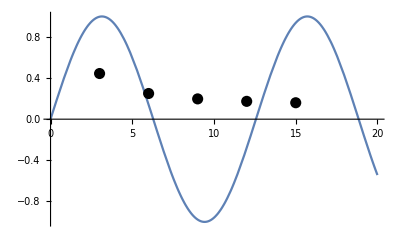

```mathematica
Plot[
f[x],
{x,0,20},
Epilog->{
PointSize[0.02],
Point[tocke]
}
]
```

ta graf neki ni prau bi moral izgledat bolj kot x^(-1)

## 2. naloga

```mathematica
ClearAll
```

ClearAll

```mathematica
Sin[Pi/2]
```

1

```mathematica
izraz = Sin[x/2]
```

{0,Sin[π/8],1/(√2),Cos[π/8],1}

```mathematica
f[x_]=Sin[x/2]
```

Sin[x/2]

```mathematica
stevila = {0,Pi/4,Pi/2,3*Pi/4,Pi}
```

{0,π/4,π/2,(3 π)/4,π}

```mathematica
izraz/.x->stevila
```

{0,Sin[π/8],1/(√2),Cos[π/8],1}

```mathematica
f[x]/.x->stevila
```

{0,Sin[π/8],1/(√2),Cos[π/8],1}

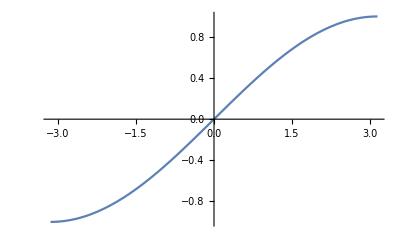

```mathematica
Plot[f[x],{x,-Pi,Pi}]
```

{{0,0},{π/4,Sin[π/8]},{π/2,1/(√2)},{(3 π)/4,Cos[π/8]},{π,1}}

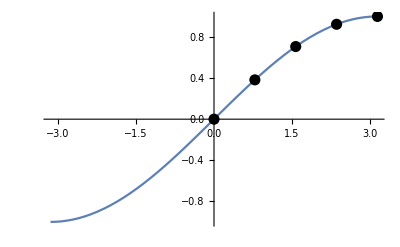

```mathematica
tocka[x_]:={x,f[x]}
tocke = Table[tocka[x],{x,stevila}]
Plot[
f[x],
{x,-Pi,Pi},
Epilog->{
PointSize[0.02],
Point[tocke]
}
]
```

## 3. naloga

```mathematica
ClearAll
```

ClearAll

```mathematica
Sin[2*Pi+Pi/4]-1/2
```

-1/2+1/(√2)

```mathematica
izraz = Sin[2*x+x/4]-1/2
```

{-1/2,-1/2+Cos[π/16],-1/2-Sin[π/8],-1/2-Cos[(3 π)/16],-1/2+1/(√2)}

```mathematica
f[x_]:=Sin[2*x+x/4]-1/2
```

```mathematica
stevila = {0,Pi/4,Pi/2,3*Pi/4,Pi}
```

{0,π/4,π/2,(3 π)/4,π}

```mathematica
f[x]/.x->stevila
```

{-1/2,-1/2+Cos[π/16],-1/2-Sin[π/8],-1/2-Cos[(3 π)/16],-1/2+1/(√2)}

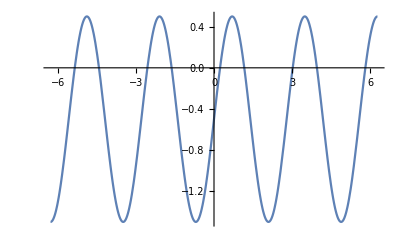

```mathematica
Plot[f[x],{x,-2*Pi,2*Pi}]
```

{{0,-1/2},{π/4,-1/2+Cos[π/16]},{π/2,-1/2-Sin[π/8]},{(3 π)/4,-1/2-Cos[(3 π)/16]},{π,-1/2+1/(√2)}}

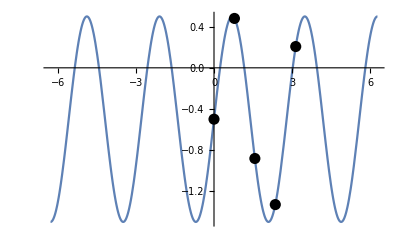

```mathematica
tocka[x_]:={x,f[x]}
tocke = Table[tocka[x],{x,stevila}]
Plot[
f[x],
{x,-2*Pi,2*Pi},
Epilog->{
PointSize[0.02],
Point[tocke]
}
]
```

ni rešena naloga do konca!

## Reševanje enačb

```mathematica
ClearAll
```

ClearAll

```mathematica
s3=Solve[y^4 ==1]
r3 = Reduce[y^4==1]
```

{{y→-1},{y→-ⅈ},{y→ⅈ},{y→1}}

y==-1||y==-ⅈ||y==ⅈ||y==1

```mathematica
f[x_]:=(x^2-CubeRoot[x^2])E^x
s4=Solve[f[y]==0]
r4=Reduce[f[y]==0]
```

{{y→-1},{y→0},{y→1}}

y==-1||y==0||y==1

```mathematica
Intersection[s3,s4]
r3&&r4//Simplify
```

{{y→-1},{y→1}}

y==-1||y==1